## Working

```mathematica
letters={"A","C","G","T"}
```

{A,C,G,T}

```mathematica
combination3=Flatten[Table[letters[[i]]<>letters[[j]]<>letters[[k]],{i,1,Length[letters]},{j,1,Length[letters]},{k,1,Length[letters]}]];
combination2=Flatten[Table[letters[[i]]<>letters[[j]],{i,1,Length[letters]},{j,1,Length[letters]}]];
```

```mathematica
genetic=<|"UUU"->"Phe","UUC"->"Phe",
"UUA"->"Leu", "UUG"->"Leu","CUU"->"Leu", "CUC"->"Leu", "CUA"->"Leu","CUG"->"Leu",
"UCU"->"Ser", "UCC"->"Ser", "UCA"->"Ser", "UCG"->"Ser","AGU"->"Ser","AGC"->"Ser",
"UAU"->"Tyr", "UAC"->"Tyr",
"UGU"->"Cys", "UGC"->"Cys",
"UGG"->"Trp",
"CCU"->"Pro","CCC"->"Pro","CCA"->"Pro","CCG"->"Pro",
"CAU"->"His","CAC"->"His",
"CAA"->"Gln","CAG"->"Gln",
"CGU"->"Arg","CGC"->"Arg","CGA"->"Arg","CGG"->"Arg","AGA"->"Arg","AGG" ->"Arg",
"AUU"->"Ile","AUC"->"Ile","AUA"->"Ile",
"AUG"->"Met",
"ACU"->"Thr","ACC"->"Thr","ACA"->"Thr","ACG"->"Thr",
"AAU"->"Asn","AAC"->"Asn","AAA"->"Asn","AAG"->"Asn",
"GUU"->"Val","GUC"->"Val","GUA"->"Val","GUG"->"Val",
"GCU"->"Ala","GCC"->"Ala","GCA"->"Ala","GCG"->"Ala",
"GAU"->"Asp","GAC"->"Asp",
"GAA"->"Glu","GAG"->"Glu",
"GGU"->"Gly","GGC"->"Gly","GGA"->"Gly","GGG" ->"Gly",
"UAA"->"STOP","UAG"->"STOP","UGA"->"STOP"
|>
```

<|UUU→Phe,UUC→Phe,UUA→Leu,UUG→Leu,CUU→Leu,CUC→Leu,CUA→Leu,CUG→Leu,UCU→Ser,UCC→Ser,UCA→Ser,UCG→Ser,AGU→Ser,AGC→Ser,UAU→Tyr,UAC→Tyr,UGU→Cys,UGC→Cys,UGG→Trp,CCU→Pro,CCC→Pro,CCA→Pro,CCG→Pro,CAU→His,CAC→His,CAA→Gln,CAG→Gln,CGU→Arg,CGC→Arg,CGA→Arg,CGG→Arg,AGA→Arg,AGG→Arg,AUU→Ile,AUC→Ile,AUA→Ile,AUG→Met,ACU→Thr,ACC→Thr,ACA→Thr,ACG→Thr,AAU→Asn,AAC→Asn,AAA→Asn,AAG→Asn,GUU→Val,GUC→Val,GUA→Val,GUG→Val,GCU→Ala,GCC→Ala,GCA→Ala,GCG→Ala,GAU→Asp,GAC→Asp,GAA→Glu,GAG→Glu,GGU→Gly,GGC→Gly,GGA→Gly,GGG→Gly,UAA→STOP,UAG→STOP,UGA→STOP|>

```mathematica
s=ReadString["C:\\Users\\walte\\OneDrive\\Documents\\Wolfram Mathematica\\sequence.fasta"]; (*Read from fasta file*)
StringLength[s]
```

30429

```mathematica
seq=DeleteMissing[Table[genetic[StringTake[s,{i,i+2}]],{i,1,StringLength[s],3}]]
Table[Take[seq,{Position[seq,"Met"][[i]][[1]],Position[seq,"STOP"][[i]][[1]]-1}],{i,1,Length[Position[seq,"STOP"]]}];
```

{Arg,Gln,Thr,Asn,Gln,Pro,Arg,Asn,Gly,Ala,Thr,Gln,Gln,Asp,Thr,Asn,Arg,Thr,Ala,Ala,Gln,His,Gly,Asp,Arg,Asn,Arg,Arg,Ala,Asn,Glu,Asn,Thr,His,Gln,Gln,Arg,Asp,Arg,Gly,Gly,Arg,Gly,Thr,Thr,Arg,His,Asn,Asn,Asn,Ala,Asn,Asn,Ser,Asn,Arg,Arg,Ala,Glu,Ala,Glu,Glu,Gly,Gln,Asp,Pro,Gly,Arg,Thr,Gly,Pro,Gln,Arg,Thr,Asn,Glu,Ala,Thr,Ala,Pro,Gly,Asp,Glu,Gly,Glu,Gln,Glu,Asn,Asn,Asn,Ser,Pro,Ala,Arg,Arg,Gly,His,Arg,Gln,Thr,Ala,Asn,Thr,His,Asn,Ala,Glu,Gln,Asp,Asp,Asn,Arg,Glu,Glu,Glu,His,Gly,Thr,Asn,Glu,Ala,Asp,Thr,Gly,Asn,Glu,Thr,Gly,Gln,Pro,Arg,Pro,Arg,Glu,Asn,Asn,Asn,Gly,Arg,Arg,Pro,Ala,Asn,Gln,Pro,Asn,Glu,Asn,Ala,Arg,Ala,Asn,Pro,Ala,Ala,Arg,Asn,Asn,Pro,Pro,Gln,Asn,Pro,Ala,His,Glu,Thr,Ala,Arg,Pro,Glu,Asn,Gly,Glu,Ala,Thr,Gly,Ser,Asn,Asn,Thr,Gly,Glu,Glu,Asp,Pro,Asn,Arg,Glu,Gln,Gln,Arg,Pro,Pro,Gln,Asn,Asn,Asn,Ala,Asn,Gln,Glu,Asn,Thr,Asn,Gly,Asn,Asn,Asn,Glu,Thr,Glu,Glu,Arg,Gly,Gln,Pro,Ala,Asn,Asn,Arg,Arg,Thr,Gly,Gln,Arg,Thr,Gly,Gln,Gly,Arg,Asp,Ala,Thr,Ala,Asn,Asn,Asn,Pro,Gly,Asn,Arg,Asn,Glu,Glu,Arg,Asp,Glu,Asn,Thr,Glu,Arg,Thr,His,Asn,Gly,Gly,Glu,Asp,Glu,Asn,Asn,Glu,Thr,Thr,His,Asn,Gly,Arg,Asn,Asn,Arg,Glu,Glu,Gly,Ala,Asn,Ser,Pro,Asn,Arg,Arg,Gly,Arg,Asn,His,Arg,Gln,Arg,Asn,Asn,Asn,Asn,Asn,Asn,Pro,Thr,Pro,Asn,Gly,Glu,Asn,Asp,Thr,Glu,Asn,Thr,Asn,Asn,Gln,His,Gln,Arg,Arg,Thr,Asn,Asn,Thr,Asn,Asn,Thr,Arg,Asn,Glu,Arg,Asn,Glu,Asn,Ala,Thr,Glu,Thr,Glu,Arg,Gly,Arg,Asn,Asn,Ala,Thr,Thr,Ala,Gly,Pro,Glu,Glu,Glu,Glu,Glu,Glu,Arg,Ala,Asn,Arg,Pro,Arg,Thr,Gly,Pro,Asn,Asn,Asn,Ser,Asn,Asn,Asn,Gln,Gln,Gln,Asp,Gly,Glu,Asp,Gln,Thr,Gln,Thr,Glu,Thr,Arg,Gly,Thr,Asp,Glu,Asn,Thr,Thr,Asn,Gln,Thr,Asn,Asn,Asn,Arg,Asn,Gln,Ala,Ala,Asn,Gly,Gly,Ala,Gly,Ala,Asn,Gln,Ala,Ser,Thr,Gly,Ala,Asp,Thr,Asn,Ala,Gln,Thr,Asn,Glu,Asp,Gln,Asn,Glu,Gln,His,Glu,Ala,Pro,Ser,Pro,Thr,Asn,Arg,His,Asn,Asn,Thr,Asn,Gln,Asn,Arg,Glu,Asn,Gln,Glu,Gln,Asn,Glu,Asn,Glu,Glu,Asn,Pro,Glu,Thr,Thr,Glu,Asn,Thr,Arg,Glu,Gln,Ser,Arg,Asn,Asn,Asn,Asn,Gln,Asn,Thr,Ala,Ala,Asp,Asp,Asn,Asn,Pro,Arg,Gly,Asn,Thr,Asn,Gly,His,Arg,Asn,Glu,Asn,Gln,Gln,Thr,Pro,Thr,Arg,Arg,Glu,Glu,Ala,Asn,Thr,Asn,Asn,Asn,Ala,Pro,Glu,Ala,Arg,Asn,Glu,Ala,Arg,Thr,Asn,Asn,His,Ala,Asn,Asn,Pro,Gln,Ser,Asn,Asn,Gln,Glu,Arg,Thr,Asn,Asn,Ser,Gln,His,Arg,Asn,Asn,Ala,His,Asn,Asn,Asn,Gln,Gln,Thr,Ala,Asn,Thr,Glu,Thr,Asn,Arg,Thr,Thr,Arg,Glu,Asn,Thr,Pro,Glu,Thr,Asp,Asn,Thr,Arg,Glu,Arg,Asn,Arg,Gln,Pro,His,Ala,Gly,Asp,Thr,Gln,Glu,Asn,Asn,His,Asn,Asn,Thr,Asp,Glu,Glu,His,Thr,Gly,Ser,Asn,His,Asn,Glu,Pro,Thr,Gly,Gln,Thr,Pro,His,Asn,Glu,Asn,Pro,Gln,Arg,Ala,Arg,Glu,Ser,Asp,Arg,Arg,Arg,Asn,Asn,Pro,Ala,Asn,Glu,Thr,Asn,Gly,Gln,Gln,Gln,Thr,Thr,Asn,Glu,Gly,Thr,Glu,Gln,Glu,Arg,Thr,Thr,Ser,Asn,Thr,Thr,Gly,Gln,His,His,Asn,Ser,Glu,Gln,His,Asn,Asn,Glu,Arg,Asn,Arg,Gln,Arg,Gly,Gln,Arg,Asn,Gln,Thr,Gln,Gln,Pro,Asn,Gln,Gln,Asn,Thr,Asp,Asn,Asn,Asp,Thr,Glu,Gln,Pro,Pro,Asn,Gln,Asn,Arg,Asn,Arg,Gln,Asn,Arg,Asn,Gln,Glu,Ser,Asn,Asn,His,Thr,Pro,Asn,Asn,Gly,Asn,Asn,Ala,Gln,Asn,Ser,His,Thr,Asn,Thr,Gly,Ala,Gln,Asn,Gln,Asn,Gln,Gln,Arg,Thr,Arg,Arg,Ala,Glu,Asn,Pro,Glu,Glu,Glu,Thr,Gln,Arg,Glu,Asn,Arg,Arg,Arg,Thr,Ser,Asn,Asn,Gln,Asn,Arg,Ala,Thr,Gln,Thr,Asn,Asn,Glu,Arg,Asn,Thr,Pro,Gly,Ser,Ala,Gln,Thr,His,Thr,Gln,Arg,Thr,Arg,Asn,Ala,Pro,Asn,Glu,Glu,Arg,Arg,Gly,Glu,Thr,Asn,Ala,Thr,Gly,Arg,Glu,Glu,His,Asn,Thr,Thr,Asn,Asn,Pro,Gly,Ala,Glu,Ala,Arg,Gly,Ala,Gln,Thr,Gly,Asn,Pro,Arg,Gln,Glu,Thr,Ala,Asn,Asp,Gln,Thr,Ser,Asn,Asn,Arg,Asn,Asn,Glu,Asn,Ala,Asn,Thr,Gly,Thr,Thr,Glu,Ala,Arg,Asp,Gln,Asn,Thr,Asn,Pro,Glu,Glu,Pro,Asn,Asn,Arg,Asn,Asp,Asn,Arg,Asn,Asn,Asn,Asn,Arg,Asn,Ser,Gln,Thr,Arg,Arg,Asn,Gln,Asn,Thr,Thr,Asn,Pro,Glu,Asn,Asn,Thr,Ala,Ala,Glu,Asn,Glu,Arg,Gln,Ser,Ser,Ala,Arg,Gln,Asn,Asn,His,Thr,Asn,Gly,Asn,Thr,Asn,Asn,Glu,Asn,Thr,Pro,Asp,Ala,Ala,Ser,Asn,Asn,Gln,Gly,Thr,Asn,Asn,Asn,Glu,Asn,Asn,Asn,Asn,Asn,Thr,Ala,Arg,Gln,Thr,Thr,Asn,Gly,Glu,Ala,His,Asn,Gln,Gly,Asn,Asp,Ala,Thr,Gln,Thr,His,Pro,Ala,Gln,Ser,Pro,Gln,Gln,Glu,Asn,Ala,Arg,Thr,Asp,Arg,Ala,Asn,Thr,Asn,Arg,His,Asn,Ser,Gly,Asn,Ser,Gln,Pro,Asn,Glu,Arg,Asp,Thr,Gly,Gln,Asn,Thr,Arg,Asn,Asn,Ala,Arg,His,Asn,Asn,Gly,Thr,Thr,Gly,Thr,Pro,Gln,Gly,Ser,Ser,Ser,Asn,Glu,Glu,Thr,Thr,Pro,Asp,Ser,Thr,His,Gly,Gln,Pro,Gln,Ser,Asn,Arg,Glu,Glu,His,Asn,Arg,Asn,Ala,Thr,Thr,Glu,Gln,Gln,Arg,Glu,Ala,Asn,Asp,Asn,Pro,Thr,Thr,Thr,Asn,His,Ser,Ala,Glu,Asn,Gly,Pro,Asn,Arg,Asn,Gln,His,Thr,Gly,Asp,Pro,Arg,Thr,Glu,Asp,Asn,Glu,Thr,Gly,Gln,Asn,Ser,Arg,Gln,Pro,Arg,His,Arg,Gln,Pro,Gly,Gln,Pro,Pro,Glu,Ala,Gln,His,Gly,Thr,Thr,Thr,Gln,Glu,Gly,Thr,Asp,Glu,Asn,Gly,Asp,Arg,Gln,Thr,Ala,Gln,Ala,Gly,His,Asn,Ser,Arg,Asn,Arg,Gln,Pro,Gln,Thr,Thr,Asn,Thr,Gln,Asp,Asp,Gly,Gln,Gly,Ala,Asn,Arg,Ala,Asn,Glu,Thr,Gly,Arg,Arg,His,Asp,Gln,Asn,Gln,Asn,Glu,Asn,Thr,His,His,Thr,Gln,Asn,Thr,Gly,Gln,Asn,Ser,Thr,Asn,Arg,Ser,Gln,Gln,Glu,Gly,Glu,Gly,His,Thr,Asn,Gln,Ala,Arg,Asn,Gly,Gln,Arg,Ala,His,Gly,Gly,Asn,Arg,Arg,Thr,Gly,Glu,Thr,Gly,Pro,Thr,Gln,Ala,Asn,Thr,Ala,Asn,Asn,Ala,Gln,Asn,Asn,Thr,Gln,Gln,Gln,Arg,Gly,Pro,Thr,Gln,Ser,Asn,Asn,Asn,His,Pro,Arg,Asp,Asn,Asn,Glu,Glu,Asp,Asn,Arg,Ala,Thr,Gln,Ala,Glu,Ser,Arg,Ser,Ala,Gly,Asn,Asn,Arg,Thr,Ala,Gln,Asn,Glu,Asn,Gln,Thr,Gln,Asn,Gln,Arg,Gly,Gln,Glu,Gly,Asn,Ala,Asp,His,Asn,Gly,His,Thr,Thr,Thr,Gln,Glu,Thr,Thr,Ala,Ala,Asn,Pro,Asp,Asn,Thr,Asn,Thr,Thr,Thr,Ser,Gly,Pro,Thr,Arg,Arg,Asn,Thr,His,Gly,Gln,Gly,Pro,Asn,Gln,Glu,Ala,Arg,Gln,Ala,Thr,Asn,His,Gln,Ser,Gln,His,Asn,Asn,Gly,Arg,His,Pro,Arg,Gly,Arg,Glu,Thr,Glu,Glu,Pro,Arg,Thr,Asp,Thr,Asn,Asn,Asn,Arg,Asn,Gln,Asn,Arg,Ser,His,Thr,Asn,Gln,Gln,Asn,Pro,Gln,Asn,Asn,Gly,Gly,Gln,Pro,Asn,Thr,His,Gly,Asn,Thr,Gly,Ser,Gln,Gly,Arg,Ala,Ala,Thr,Gln,Asn,Asn,Asn,Gln,Thr,Asp,Thr,Asn,Asn,Thr,Arg,Glu,Arg,Pro,Arg,Thr,Gln,His,Thr,Arg,Asn,Ser,Pro,Thr,Arg,Gln,Ala,Thr,Gly,Thr,Thr,Asn,Asn,Arg,Gln,Glu,Asn,Asp,Glu,Asp,Glu,Thr,His,Pro,Thr,Arg,Asn,Gly,Gln,Asn,Glu,Thr,Thr,His,His,Asn,Thr,Ala,Asp,Arg,Glu,Asp,Asn,Arg,His,Gln,Gln,Asn,Gly,Asn,Thr,Gln,Ala,Thr,Pro,Asn,Ala,Asn,Asn,Thr,Gln,Ala,Arg,Thr,Gln,Gln,Arg,Thr,Asn,His,Ala,Arg,Pro,Gly,Gln,His,Asp,Asp,Thr,Asn,Asn,Asn,Asp,Thr,Glu,Glu,Arg,Pro,Gly,Asp,Pro,Pro,Asn,Gly,Thr,Ala,Gln,Gln,His,Gln,Pro,Arg,Asn,Pro,Gly,His,Arg,Glu,Arg,Thr,Gly,Asn,Thr,Gly,Thr,Thr,Asn,Ala,Ala,Asn,Gln,Asn,Pro,Asn,Asn,Asp,Gly,Gly,Arg,Asn,Asn,Thr,Arg,Ala,Gln,Gln,Gln,Glu,Asn,Gly,Pro,Gln,Gln,Arg,Gln,Ser,Gly,Gly,Gln,Arg,Asn,His,Gln,Asn,Gln,Asn,Ala,Ala,Asn,Arg,Arg,Thr,Asp,Gln,Thr,Asn,Glu,Ser,Arg,His,Glu,Glu,Gln,Ala,Gly,Thr,Thr,Asn,Glu,Asn,His,Asn,Arg,Ala,Asn,Gly,Gln,Thr,Asn,Thr,Pro,Asn,Asn,Ala,His,Asn,Gly,Thr,Gly,Ala,Thr,Asn,Gln,Gly,Gln,Gln,Arg,Pro,Gln,Asn,Thr,Asp,Glu,Glu,Thr,Gln,Thr,Asn,Asp,Ser,Arg,Gly,Asn,Glu,Asn,Gln,Asn,Gln,Gly,Arg,Thr,Asn,Asp,Asn,Asn,Gln,Pro,Pro,Arg,Gly,Ala,Arg,Asn,Asn,Arg,Thr,Ser,Thr,His,Asn,Arg,Arg,Asn,Glu,Thr,Gly,His,Asp,His,Asn,Gly,Thr,Gly,His,Thr,Ala,Thr,Gly,Gly,Ala,His,Arg,Ala,Asp,Asn,Asp,Thr,Asn,Pro,Gln,Arg,His,Arg,Asp,Arg,Arg,Glu,His,Asn,His,Pro,Asp,Asn,Asn,Thr,Ser,Asp,Ala,Ala,Thr,Asp,Thr,Ser,His,Asn,Gln,Ser,Arg,Asn,Gln,Ser,Arg,Arg,Asn,Asn,Thr,Glu,Glu,Asn,Arg,Pro,Pro,Asn,Arg,Asn,Gln,Thr,Arg,Arg,His,Asn,Arg,Glu,Gln,Gln,Thr,His,Gln,Ala,Thr,Pro,Gln,Glu,His,Arg,Gly,Pro,Thr,Arg,Gln,Asn,Asn,Ala,Asn,Pro,Asp,His,Arg,Ala,Thr,Ala,Thr,Ala,Ala,Glu,Asn,Ala,Asn,Thr,Thr,Arg,Gln,Glu,Asn,Asn,Arg,Arg,Gln,Gln,Ala,Thr,Ala,Arg,Asn,His,Arg,Pro,Thr,Thr,Thr,His,Asn,Gly,His,Arg,Thr,Arg,Gln,Asp,Asn,Gln,Thr,Glu,Gly,Glu,Asp,Asn,Asn,Ala,Asn,Asp,Asn,Gly,His,Ala,Gln,Ala,Asn,Ala,Glu,His,Thr,Gly,Glu,Asn,His,Gln,Ala,Asn,Gly,Pro,Gln,Gln,Gly,Arg,His,Asn,His,Asn,Ser,Asn,Gln,Pro,Glu,Gln,Asn,Ala,Ala,Glu,Thr,Thr,Gln,Thr,Glu,Pro,Arg,Ala,Gln,Glu,Thr,Gly,Arg,His,Thr,Thr,Gly,Thr,Thr,Gln,Asn,Asn,Thr,Ala,Arg,Thr,Glu,Asp,Asn,Gln,Asn,Thr,Arg,Glu,Ser,Asn,Thr,Thr,Arg,Arg,Gly,Arg,Ser,Pro,Ser,Gln,Thr,Gln,Thr,Thr,Arg,Asn,Pro,Pro,Gly,Gln,Asn,Thr,Gln,Arg,Glu,Ala,Asn,Thr,Thr,His,Asn,Thr,Glu,Gly,His,Asn,Asn,Gly,Glu,Arg,Thr,Arg,Ala,Thr,His,Arg,His,Ala,Asn,Gly,Gln,Thr,Asn,Ala,Thr,Asn,Ala,Ala,Arg,His,Glu,Ala,Asp,Glu,Gly,Arg,Asn,Thr,Asn,Gln,Thr,Gln,Thr,Thr,Asn,Asn,Gln,Glu,Asn,Ala,Gln,Gln,Ser,Arg,Arg,His,Thr,Gln,His,Arg,Ala,Gly,Ala,Pro,Thr,Asn,Asn,Gly,Asn,Ala,His,Thr,Ser,Asn,Asn,Thr,Thr,Gln,Glu,Asn,Asn,Gln,His,Thr,Arg,Glu,Arg,Ser,Gln,Thr,Thr,Gln,Asp,Arg,Asn,Arg,Asp,Gln,Gln,Glu,Pro,Asn,Thr,Asn,Asn,Asn,Asn,Thr,Ser,Gly,Ala,Gln,Asn,Gln,Gln,Arg,Asn,Thr,Gly,Asn,Arg,Pro,Ala,Asp,Ala,Asn,Asn,Asn,Asn,Thr,His,Arg,Glu,Pro,Gln,Asn,Asn,Asn,Asn,Gln,Gly,Thr,Gly,Glu,Ala,Asn,Thr,Gln,Asn,Pro,Thr,Thr,Asn,Glu,Asn,Thr,Arg,Asn,Pro,Gly,Asn,Asn,Asn,Glu,Gly,Ala,Glu,Gly,Gln,Ser,Thr,Gly,Thr,Arg,Arg,Gly,Gln,Gln,Asn,Gln,Arg,Asn,Gln,Glu,Asn,Gln,Asn,Asn,Arg,Arg,Pro,Arg,Asn,Pro,Asn,Gly,Asn,Arg,Thr,Asn,Asn,Glu,Glu,Asn,Asp,Gln,Ala,Thr,Asn,Gly,Asn,Asn,His,Asn,Ser,Thr,Glu,Asn,Glu,His,Gln,Gln,Asp,Thr,Asp,Ala,Asn,Thr,Ser,Gly,Arg,Pro,Asp,Gln,Asn,Asn,Asn,Arg,Thr,Asn,Asn,Ser,Gly,Asn,Thr,Glu,Asn,Thr,Arg,Asp,Ser,Glu,Ser,Ala,Asn,His,Ala,Asn,Asn,Gln,Thr,Arg,Thr,Pro,Gln,Asp,Asn,Pro,Asn,Gly,Asn,Arg,Arg,Gln,Asp,Glu,Asn,Thr,Thr,Glu,Thr,Asn,Arg,Ala,Asn,Gln,Asn,Pro,Thr,His,Thr,Thr,Asn,Gln,Asp,Asp,Gln,Glu,Pro,Thr,Pro,Arg,Thr,Glu,Gly,Arg,Arg,Pro,Asn,Asn,Glu,Gln,Pro,Gly,Pro,Gln,Asn,Gln,Gln,Asn,Gly,Asn,Gln,Ala,Ser,Thr,Asn,Glu,Asn,Arg,Asn,Arg,Glu,Asn,Asn,Asn,His,Thr,Ala,Pro,Gly,Gly,Arg,Thr,Arg,Ala,Arg,Thr,Asn,Glu,Thr,Ala,Gln,Arg,Asn,Asn,Asn,Arg,Arg,Pro,Arg,Asn,Asn,Asn,Asn,Glu,Asn,Glu,Asn,Gln,Gln,Arg,Thr,Asn,Glu,Asn,Ala,Thr,Arg,Ala,Glu,Gln,Glu,Glu,Gln,Gln,Arg,Pro,Glu,Ala,Arg,Glu,Arg,Gln,Pro,Gly,Gln,Gly,Asn,Thr,Arg,Arg,Ser,Glu,Gln,Arg,Thr,Gly,Asn,Arg,Glu,Gln,Ala,Ser,Thr,Glu,Thr,Pro,Thr,His,Pro,Thr,Gln,Asn,His,Gln,Gln,Asp,Asn,Asn,Asn,Asn,Thr,Gly,Thr,Glu,Asn,Asn,Asn,Ala,Pro,Thr,Gln,Arg,His,Pro,Thr,Asp,Thr,His,His,Gln,Glu,Gln,Gln,Gln,Asn,Thr,Glu,Ala,Gln,Ala,Arg,Asn,Thr,Arg,Arg,Gly,Asn,Thr,Thr,Pro,Gln,Ala,Arg,Gln,Arg,Arg,Ala,Gln,Ala,Arg,Asn,Thr,His,Asn,Gln,Asn,Gln,Pro,Arg,Gln,Gln,Thr,Glu,Ser,Gln,Gly,Thr,Gln,Asn,Gly,Ser,Thr,Arg,Gln,Asn,His,Pro,Arg,Thr,Gln,Thr,Gln,Asn,Thr,Thr,Asn,His,Asn,Gln,Gln,Asn,Gln,Ala,Arg,Glu,Asn,Asn,Thr,Ala,Gly,Asn,Gln,Arg,Thr,Asn,Arg,Ala,Thr,Gln,Asn,Thr,His,Arg,Gln,Thr,Ala,Ala,Gln,Pro,Gln,Arg,Thr,Glu,Glu,Pro,Asn,Gln,Pro,Gln,Asn,His,Pro,Gln,Gln,His,Glu,Asn,Asn,Thr,Asn,Gln,Asn,Thr,Asn,Gln,Ser,Ala,Thr,Gln,Gly,Ala,His,Arg,Gln,Asn,Arg,Asn,Glu,Gln,Asn,Glu,Asn,Glu,Gly,Gln,Asn,Arg,Gly,Asn,Gly,Pro,Ser,Thr,Ala,Asp,Pro,Thr,Arg,Asn,Gln,Pro,Glu,Asn,His,Asn,Gly,Thr,His,Thr,Gln,Arg,Glu,Pro,Gln,Thr,Asp,Asn,Arg,Gln,Gln,His,Ala,Thr,Arg,Arg,Arg,His,Gln,Asp,Gly,Asn,Gln,Asn,Glu,Asp,Arg,Glu,Gln,Glu,Asn,Arg,Pro,Arg,Asn,Ala,Asn,Ala,Thr,Gly,Pro,Gln,Thr,Asn,Gly,Gly,Asn,Glu,Asp,Ala,Gln,Arg,Gln,Thr,His,Asn,Glu,Arg,His,Asn,Asn,Glu,Ala,Arg,Gln,Gly,Arg,Ala,Gln,Arg,Arg,Asn,His,Gly,Ala,His,Gln,Ser,Asn,Thr,Asn,Asn,Arg,Gln,Ala,Asn,Gln,Asn,Thr,Ala,Asn,Pro,Arg,Glu,Arg,Asn,Asn,Asn,Pro,Ala,Asn,Ala,Arg,Thr,Gln,Asn,Gln,Ala,Gln,Gln,Asn,Thr,Arg,Asn,Glu,Gly,Asn,Asp,His,Asp,Gln,Glu,Arg,His,Thr,Gln,Asn,Asn,Asn,Thr,Gln,Thr,Pro,Glu,Gln,Asn,Gln,Glu,Pro,Thr,Thr,Ser,Ala,Gln,Glu,Glu,Gly,Arg,Asp,Arg,His,Pro,Arg,Ala,Thr,Asn,Asn,Arg,Asn,Glu,Gly,Ala,Ala,Gln,Arg,Arg,Asn,Thr,Glu,Arg,Gly,Pro,Thr,Gly,Pro,Arg,Asn,His,Arg,Arg,Gly,Arg,Gln,Asp,Arg,Arg,Pro,Gln,Asn,Thr,Asn,Pro,Gly,Thr,Arg,Pro,Glu,Glu,Gly,Thr,Thr,Pro,Arg,Thr,Gln,Gly,Ala,Asn,His,Glu,Arg,Thr,Glu,Arg,Ser,Gln,Ala,Arg,Arg,Gly,Asn,Asn,Asn,Thr,Asp,Gln,Gln,Thr,Asp,Asn,Arg,Arg,Ala,Glu,Arg,Asn,Asn,Asn,Glu,Arg,Arg,Ala,Gln,Arg,Asn,Arg,Thr,Asn,His,His,His,Gln,Glu,Arg,Thr,Thr,Asn,Glu,Gly,Thr,Arg,Gly,Gln,Thr,Ser,Gln,Asp,His,Thr,Ala,Asn,Thr,Pro,Gln,His,Asn,Arg,Gln,Glu,Glu,Gln,Glu,Pro,Ala,Ala,Asn,His,Gln,Asn,Asn,Asp,Arg,Glu,Asp,Ser,Ala,Asn,Thr,Asn,Arg,Thr,Glu,Gln,Ala,His,Gln,Glu,Gln,Gln,Gln,Pro,Asp,Arg,Ser,Asn,Ser,Thr,Ala,Arg,His,Pro,Thr,Gln,Thr,Gln,Glu,Asn,Arg,Arg,Arg,Asn,Glu,Gln,Asn,Thr,Pro,Asn,Ala,Asn,Thr,Pro,Thr,Arg,Asn,Gln,Thr,Arg,Glu,Asn,Ala,Gly,Arg,Gln,Asn,Asn,Gly,Pro,Asn,Pro,Ala,Thr,Gln,Gly,Asn,Glu,Asp,Asn,Arg,Gly,Gln,Gly,His,Gln,Gln,Arg,Pro,Pro,Asn,Ser,Gln,Thr,Thr,Asn,Asn,Gln,Thr,Glu,Gly,Gln,Asn,Gly,Pro,Asn,Asn,Asp,Gly,Ala,Glu,Gly,Ala,Thr,Pro,Arg,His,Pro,Gln,Gln,Thr,Arg,Asn,Asn,Gln,Asn,Thr,Gln,Asn,Gly,Ala,Glu,Ala,Ala,Asn,His,Arg,Asn,Arg,Pro,Gly,Ser,Arg,Gly,Arg,Gly,Arg,Gln,Glu,Pro,Glu,Gln,Asn,Ala,Asn,Asn,Asn,Asn,Ala,Asn,Arg,Arg,Arg,Ser,Gln,Asn,Ala,Asn,Ala,Thr,Gln,Gly,Arg,Pro,Glu,Gln,Thr,Arg,Asn,Gly,Pro,Gly,Gln,Thr,Arg,Asn,Gln,Thr,Ala,Ala,Thr,Pro,Pro,Ala,Gln,Glu,Arg,Ala,Ala,Asn,His,Arg,Glu,Thr,Thr,Ala,Asn,Asp,Asn,Pro,Asn,Gln,Glu,Ala,Arg,Gln,Asn,Pro,Thr,Asn,Arg,Ala,Asn,Gly,Gln,Asn,Glu,Glu,Gly,Asn,Asn,Arg,Arg,Asp,Arg,Arg,Asn,Ser,Asn,Gln,Asn,Gln,Gln,Gln,Ser,Asp,Gln,Ala,Arg,Pro,His,Asn,Ala,Gly,Asn,Arg,Ala,Glu,Thr,His,Asn,Ser,Gly,Gly,Glu,Arg,Ala,Thr,Thr,Pro,Arg,Pro,Arg,Gly,Glu,Thr,Asn,Arg,Glu,Ser,Gly,Arg,Ala,Asn,Pro,Glu,Asp,Asn,Asn,Asn,Asn,Asn,Asn,Asn,Asn,Asn,Asn}

```mathematica
genes=DeleteDuplicates[Values[genetic]]
```

{Phe,Leu,Ser,Tyr,Cys,Trp,Pro,His,Gln,Arg,Ile,Met,Thr,Asn,Val,Ala,Asp,Glu,Gly,STOP}

```mathematica
distribution =Table[{genes[[i]],Count[seq,genes[[i]]]},{i,1,Length[genes]}]
```

{{Phe,0},{Leu,0},{Ser,87},{Tyr,0},{Cys,0},{Trp,0},{Pro,179},{His,144},{Gln,378},{Arg,375},{Ile,0},{Met,0},{Thr,413},{Asn,679},{Val,0},{Ala,233},{Asp,109},{Glu,274},{Gly,218},{STOP,0}}

```mathematica
distributionBlind=Table[Count[seq,genes[[i]]],{i,1,Length[genes]}]
```

{0,0,87,0,0,0,179,144,378,375,0,0,413,679,0,233,109,274,218,0}

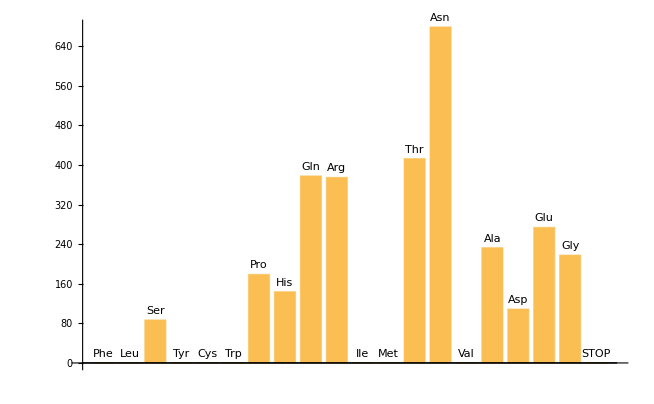

```mathematica
BarChart[distributionBlind,ChartLabels->Placed[genes,Above]]
```